```mathematica
opi=turboBoundary@@@
```

```mathematica
cr=compressorRequirement/@opi;
```

```mathematica
etacs=readMapEtaV[cr,mapList[[6]]]
```

{0.699402,0.707777}

```mathematica
tr=turbineRequirement@@@Transpose[{cr,etacs}];
```

```mathematica
etats={0.65,0.68}
wgs={0,0.1}
```

{0.65,0.68}

{0,0.1}

```mathematica
tt=turbineTuning@@@Transpose[{tr,wgs,etats}];
```

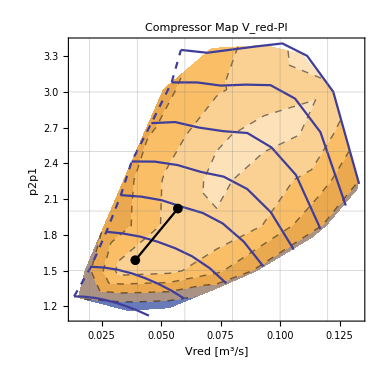
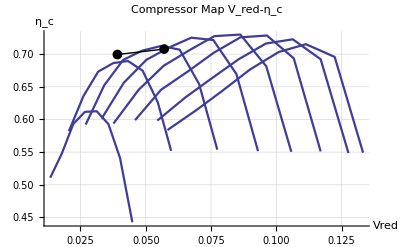

```mathematica
matchingCompressor[tt,mapList[[6]]]
```

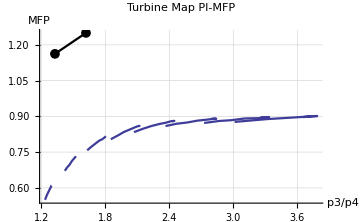
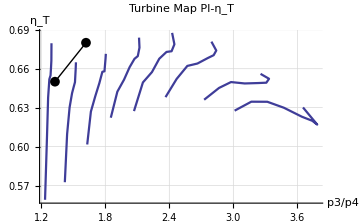

```mathematica
matchingTurbine[tt,mapList[[6]]]
```